```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions={θ<π/2, θ>-π/2,d>0,ϵ>0};
```

```mathematica
df[ζ_]=k (1+d^2/ζ^2)^(θ/π);
f[ζ_]=c+ k(ζ/d)^(1-2 θ/π)  Hypergeometric2F1[-θ/π,1/2-θ/π,3/2-θ/π,-ζ^2/d^2];
(*f[ζ_]=∫df[ζ]ⅆζ+c//Simplify*)
```

```mathematica
(*Limit[f[ϵ],ϵ->0,Direction->-1]//Simplify*)
```

```mathematica
(*Limit[f[ϵ-ⅈ d],ϵ->0,Direction->-1]//Simplify*)
```

```mathematica
(* Condition for d: Re@f[L]=L when L->∞ *)
Limit[(Re@f[L])/L,L->∞](*==1*)
```

((π-2 θ) Re[k])/(d π)

```mathematica
d=(k (π-2 θ))/π;
```

```mathematica
(* 
dz: height hinge to y=0
du: height y=0 to horizontal mirror
du+dz = flap height.
*)
```

```mathematica
c=-(dz+du) Tan[θ]+ⅈ du;
k=(π √π)/(π-2 θ)((dz-ⅈ c) ⅇ^(-ⅈ θ))/(Gamma[1+θ/π] Gamma[1/2-θ/π]);
```

```mathematica
Block[{dz=.6,du = .0,θ =20*π/180},{f[.00001],f[-ⅈ d+.000001]}]
```

{-0.218238+0. ⅈ,2.21622×10^-7-0.6 ⅈ}

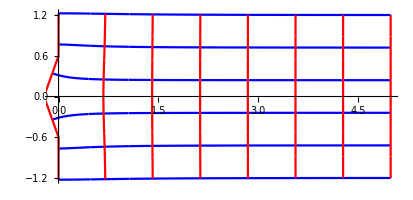

```mathematica
Block[{dz=.6,du = .0,θ =20*π/180,lim={.00001,5,-1.2,1.2}},
Show[ParametricPlot[Array[ReIm@f[ξ+ⅈ #]&,6,lim⟦{3,4}⟧],{ξ,lim⟦1⟧,lim⟦2⟧},PlotStyle->{Blue},AspectRatio->Automatic],
 ParametricPlot[Array[ReIm@f[#+ⅈ η]&,8,lim⟦{1,2}⟧],{η,lim⟦3⟧,lim⟦4⟧},PlotStyle->{Red},AspectRatio->Automatic]]]
```

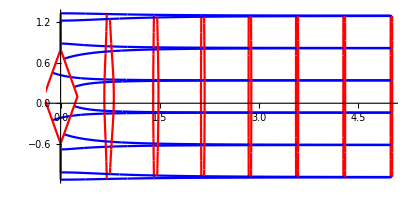

```mathematica
Show[Block[{dz=.6,du = .1,L=20,θ =20*π/180,lim={.00001,5,-1.2,1.2}},
Show[ParametricPlot[Array[ReIm@f[ξ+ⅈ #]&,6,lim⟦{3,4}⟧],{ξ,lim⟦1⟧,lim⟦2⟧},PlotStyle->{Blue},AspectRatio->Automatic],
 ParametricPlot[Array[ReIm@f[#+ⅈ η]&,8,lim⟦{1,2}⟧],{η,lim⟦3⟧,lim⟦4⟧},PlotStyle->{Red},AspectRatio->Automatic]]],Block[{dz=.6,du = .1,L=20,θ =-20*π/180,lim={.00001,5,-1.2,1.2}},
Show[ParametricPlot[Array[ReIm@f[ξ+ⅈ #]&,6,lim⟦{3,4}⟧],{ξ,lim⟦1⟧,lim⟦2⟧},PlotStyle->{Blue},AspectRatio->Automatic],
 ParametricPlot[Array[ReIm@f[#+ⅈ η]&,8,lim⟦{1,2}⟧],{η,lim⟦3⟧,lim⟦4⟧},PlotStyle->{Red},AspectRatio->Automatic]]]]
```